```mathematica
titiusbode[p_] := With[
{x=PlanetData["Earth","SemimajorAxis"],y=2^(p-1)UnitStep[p-1]},
x(3y+4)/10]
```

```mathematica
data=Last@Outer[PlanetData,{#},{"SemimajorAxis","Name"}]&/@PlanetData[];
(* Get semi-major axis of every planet *)
```

```mathematica
belt={"Asteroid Belt",
Mean[LinguisticAssistant]};
```

```mathematica
(* Since Pluto is not a planet anymore, its data is added separately *)
(* Also the mean-distance of asteroid belt is needed as well. *)
data=Insert[data,
{EntityClass["MinorPlanet",#]@"SemimajorAxis"//Mean,#}&["AsteroidBelt"],
5];
AppendTo[data,MinorPlanetData["Pluto",#]&/@{"SemimajorAxis","Name"}];
```

```mathematica
prediction=titiusbode/@Range[0,8];
names=Last/@data;
distance=First/@data;
```

#### Plot the predicted value vs. actual data

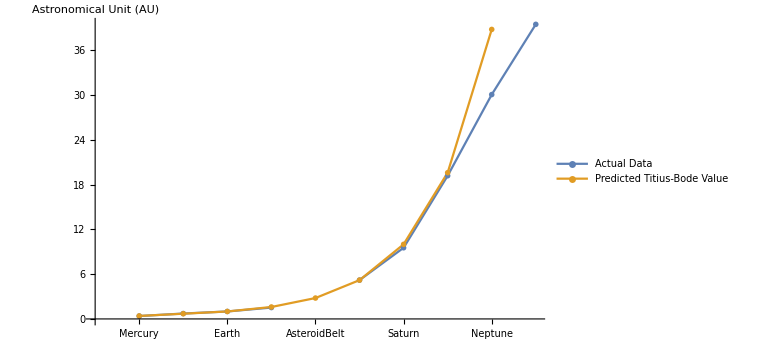

```mathematica
ListPlot[{distance, prediction}, Joined -> True, 
 Ticks -> {MapIndexed[{Tr@#2,#1}&,names], "Automatic"}, 
 ImageSize -> Large, PlotMarkers -> "OpenMarkers", 
 AxesLabel -> {None, "Astronomical Unit (AU)"}, 
 PlotLegends -> {"Actual Data", "Predicted Titius-Bode Value"}]
```

#### By ignoring the outlaying data!! of Neptune, we see an interesting pattern:

```mathematica
{distance,names}=Thread@Delete[data,9]; (* delete neptune *)
```

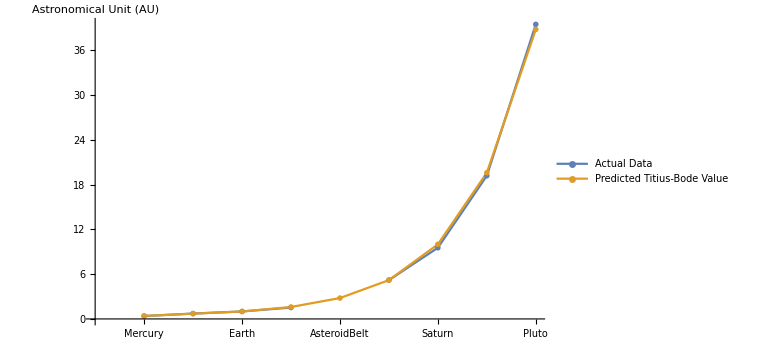

```mathematica
ListPlot[{distance, prediction}, Joined -> True, 
 Ticks -> {MapIndexed[{Tr@#2,#1}&,names], "Automatic"}, 
 ImageSize -> Large, PlotMarkers -> "OpenMarkers", 
 AxesLabel -> {None, "Astronomical Unit (AU)"}, 
 PlotLegends -> {"Actual Data", "Predicted Titius-Bode Value"}]
```